```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.25},{0.25,1.5}}],{x}]][[1]]
fDerivative[f_,z_]:=Module[{x,v},v=Array[x,Length[z]];
D[f@@v,{v}]/.Thread[v->z]]
fLeapFrogStep[θ_,m_,ϵ_,logP_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[logP,θ];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[logP,θ1];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = Union[{Cprimed},{Cprimedprimed}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstep[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};While[s==1,v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1];C]
fNUTSstepExtract[c_]:=Module[{dep=Depth@c},RandomChoice@DeleteCases[Flatten[c,dep-4],{}]]
fNUTSstepComplete[θ_,ϵ_,logP_,Δ_]:=Module[{c=fNUTSstep[θ,ϵ,logP,Δ]},fNUTSstepExtract[c]]
fNUTS[M_Integer,θ0_,ϵ_,logP_,Δ_]:=NestList[fNUTSstepComplete[#[[1]],ϵ,logP,Δ]&,{θ0,{}},M]
```

```mathematica
samples=fNUTS[50,{5,5},0.1,f,1000];
```

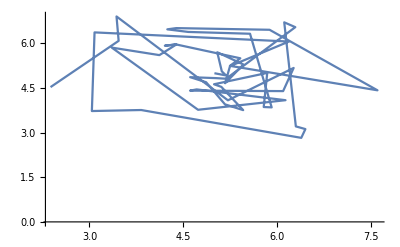

```mathematica
ListLinePlot[samples[[All,1]]]
```

## Visualising tree

```mathematica
fNUTSstepSingle[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1;C]
fNUTSstepSingleString[thetaMinus_,mMinus_,thetaPlus_,mPlus_,C_,j_,s_,u_,ϵ_,logP_,Δ_]:=Module[{thetaMinus1=thetaMinus,mMinus1=mMinus,thetaPlus1=thetaPlus,mPlus1=mPlus,s1=s,temp1,temp2,Cprimed,sprimed,v,C1,j1,dep},
v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus1,mMinus1,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus1,mMinus1,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus1,mPlus1,Cprimed,sprimed}=fBuildTree[thetaPlus1,mPlus,u,v,j,ϵ,logP,Δ]];
dep=Depth@Cprimed-4;
If[sprimed==1,C1=Join[{C},{Cprimed}]];
s1=sprimed If[(thetaPlus1-thetaMinus1).mMinus1 ≥ 0,1,0]If[(thetaPlus1-thetaMinus1).mPlus1 ≥ 0,1,0];j1 = j + 1;{thetaMinus1, mMinus1, thetaPlus1, mPlus1,C1,j1,s1,u,ϵ,logP,Δ}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{res[[1]],res[[2]],{}}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = DeleteCases[Union[{Cprimed},{Cprimedprimed}],{}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstring[theta0_,m0_,u_,ϵ_,logP_,Δ_]:=NestWhileList[fNUTSstepSingleString@@#&,{theta0,m0,theta0,m0,{theta0,m0},0,1,u,ϵ,logP,Δ},#[[7]]==1 &]
fUnravel[lTree__]:=Module[{len=(Length@lTree)-1,lDeps,lAll},lDeps=Table[Depth@lTree[[i]][[5]],{i,1,len,1}];lAll=Table[Flatten[lTree[[i]][[5]],If[lDeps[[i]]-4>0,lDeps[[i]]-4,0]],{i,1,len,1}];Table[If[i==1,{lAll[[i]]},lAll[[i]]],{i,1,len,1}]]
fMaxMins[test__]:=Module[{maxes=Max/@Thread@fUnravel[test][[Length@test-1]][[All,1]],mins=Min/@Thread@fUnravel[test][[Length@test-1]][[All,1]]},Thread[{mins-0.1,maxes+0.1}]]
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.},{0.,1.5}}],{x}]][[1]]
```

```mathematica
test=fNUTSstring[{3.5,5.3},{0.1,-0.2},0.001,0.4,f,1000];
```

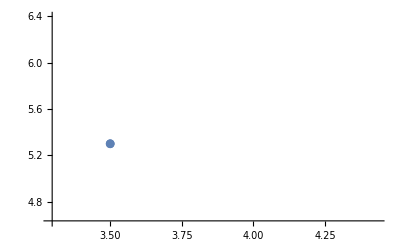
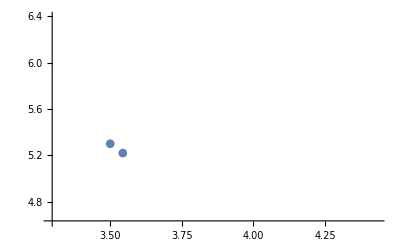
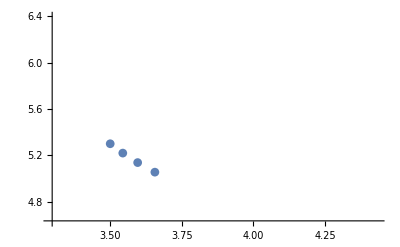
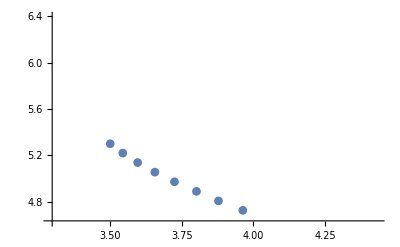
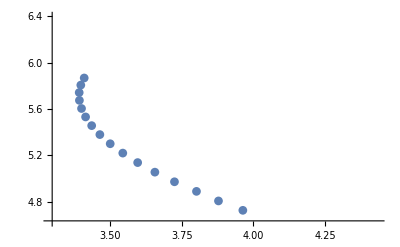
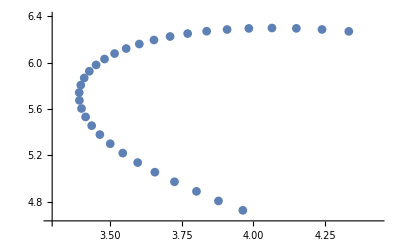

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,1]],PlotMarkers->Automatic,PlotRange->fMaxMins[test]],{i,1,Length@test-1,1}]
```

```mathematica
fDisjoint[test__]:=Table[Complement[fUnravel[test][[i]][[All,1]],Flatten[Union[Table[fUnravel[test][[j]][[All,1]],{j,1,i-1,1}]],1]],{i,1,Length@test-1,1}]
```

```mathematica
c01=RGBColor[58.4/100,38.8/100,23.9/100];
c02=RGBColor[62.4/100,63.5/100,63.1/100];
c03=RGBColor[58.0/100,41.6/100,61.2/100];
c04=RGBColor[84.3/100,36.1/100,33.7/100];
c05=RGBColor[96.1/100,71.8/100,40.8/100];
c06=RGBColor[50.2/100,67.8/100,43.5/100];
c07=RGBColor[29.0/100,50.2/100,67.1/100];
c08=RGBColor[56.1/100,57.3/100,56.9/100];
c09=RGBColor[51.4/100,34.5/100,54.5/100];
c10=RGBColor[81.2/100,27.5/100,23.5/100];
c11=RGBColor[94.9/100,67.8/100,31.0/100];
c12=RGBColor[42.7/100,62.7/100,36.1/100];
c13=RGBColor[18.8/100,43.5/100,61.6/100];
apple13={c01,c02,c03,c04,c05,c06,c07,c08,c09,c10,c11,c12,c13}
```

{RGBColor[0.584, 0.38799999999999996, 0.239],RGBColor[0.624, 0.635, 0.631],RGBColor[0.58, 0.41600000000000004, 0.612],RGBColor[0.843, 0.36100000000000004, 0.337],RGBColor[0.961, 0.718, 0.408],RGBColor[0.502, 0.6779999999999999, 0.435],RGBColor[0.29, 0.502, 0.6709999999999999],RGBColor[0.561, 0.573, 0.569],RGBColor[0.514, 0.34500000000000003, 0.545],RGBColor[0.812, 0.275, 0.23500000000000001],RGBColor[0.9490000000000001, 0.6779999999999999, 0.31],RGBColor[0.42700000000000005, 0.627, 0.36100000000000004],RGBColor[0.188, 0.435, 0.616]}

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
apple7={blue,green,yellow,Orange,red,purple,grey};
```

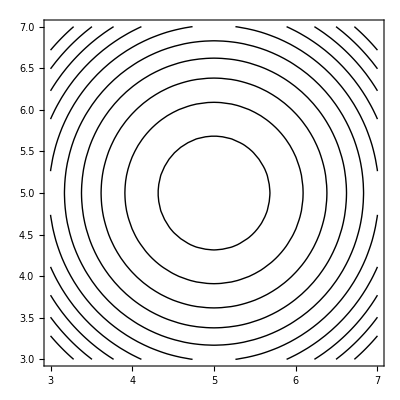

```mathematica
gMain=ContourPlot[f[{x,y}],{x,3,7},{y,3,7},ContourStyle->Black,Contours->10,ContourShading->None]
```

```mathematica
lAnimations=Table[Show[gMain,Table[ListPlot[fDisjoint[test][[i]],PlotRange->fMaxMins[test],PlotStyle->apple7[[i]]],{i,1,j,1}]],{j,1,Length@test-1,1}];
```

```mathematica
ListAnimate[lAnimations]
```

```mathematica
temp=fUnravel[test][[Length@test-1]][[All,1]];
```

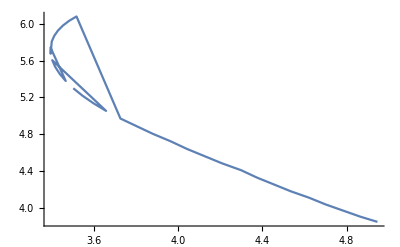

```mathematica
ListLinePlot[temp]
```

```mathematica
lorder=FindShortestTour[temp][[2]];
```

```mathematica
dists=Table[Norm[temp[[lorder]][[i+1]]-temp[[lorder]][[i]]],{i,1,Length@temp,1}]
```

{0.0870629,0.082463,0.0781729,0.0742286,0.0706633,0.0675093,0.0647979,0.0625596,0.0608226,0.0596114,0.0589448,0.0588336,2.65055,0.101091,0.105227,0.105597,0.108836,0.108193,0.109727,0.110197,0.110432,0.117305,0.115155,0.115573,0.112179,0.117572,0.112798,0.113022,0.107643,0.102284,0.0970245,0.0919323}

```mathematica
maxPos=Position[dists,Max[dists]][[1,1]]
```

13

```mathematica
lorder1=Join[lorder[[maxPos+1;;]],lorder[[1;;maxPos]]]
```

{32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,4,3,2,1,1,8,7,6,5,10,9,11,12,13,14,15,16}

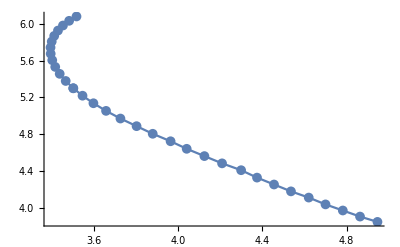

```mathematica
ListLinePlot[temp[[lorder1]],PlotMarkers->{Automatic, 10}]
```